### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
rs=FromReducedRankIndex[733448814971]
```

<|Index→733448814971,QCode→32342434232423224,RuleSet→{AA→AB,BB→AA,B→AA,A→B}|>

We can pull out the ruleset itself:

```mathematica
rs[["RuleSet"]]
```

{AA→AB,BB→AA,B→AA,A→B}

We generate the sessie and its causal network, again giving it a convenient name:


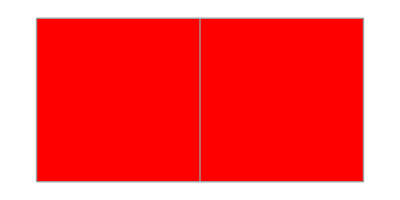

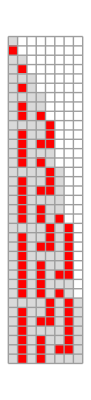
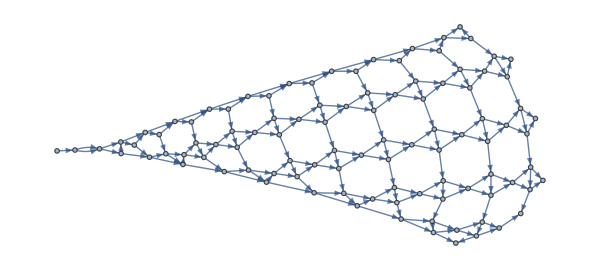
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss=SSS[rs[["RuleSet"]], "A",1000, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->35,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

```mathematica
SSSInteractiveDisplay[sss]
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss[["Net"]]//Short
```

{1→2,2→3,2→3,3→4,3→5,4→5,5→6,5→7,6→7,6→8,«1941»,994→996,945→996,996→997,945→997,996→998,997→998,997→999,948→999,999→1000,948→1000}

```mathematica
nds=ToNetDifferenceSets[sss[["Net"]]]
```

{{1},{1,1},{1,2},{1,4},{1,2},{1,2},{2,3},{3,4},{1,2},{4,5},{1,2},{1,7},{3,4},{1,2},{5,6},{1,2},{1,2},{4,5},{6,7},{1,2},{7,8},{1,2},{1,2},{6,7},{1,2},{1,10},{6,7},{1,2},{8,9},{1,2},{1,2},{7,8},{1,2},{1,2},{7,8},{9,10},{1,2},{10,11},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{1,2},{1,13},{9,10},{1,2},{11,12},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{12,13},{1,2},{13,14},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,16},{12,13},{1,2},{14,15},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{15,16},{1,2},{16,17},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,19},{15,16},{1,2},{17,18},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{18,19},{1,2},{19,20},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,22},{18,19},{1,2},{20,21},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{21,22},{1,2},{22,23},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,25},{21,22},{1,2},{23,24},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{24,25},{1,2},{25,26},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,28},{24,25},{1,2},{26,27},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{27,28},{1,2},{28,29},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,31},{27,28},{1,2},{29,30},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{30,31},{1,2},{31,32},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,34},{30,31},{1,2},{32,33},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{33,34},{1,2},{34,35},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,37},{33,34},{1,2},{35,36},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{36,37},{1,2},{37,38},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,40},{36,37},{1,2},{38,39},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{39,40},{1,2},{40,41},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,43},{39,40},{1,2},{41,42},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{42,43},{1,2},{43,44},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,46},{42,43},{1,2},{44,45},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{45,46},{1,2},{46,47},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,49},{45,46},{1,2},{47,48},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{48,49},{1,2},{49,50},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,52},{48,49},{1,2},{50,51},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{51,52},{1,2},{52,53},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1},{},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1}}

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.

```mathematica
Position[nds,{51,52}]
```

{{904},{909},{912},{915},{918},{921},{924},{927},{930},{933},{936},{939},{942},{945},{948}}

```mathematica
nds[[1;;903]]
```

{{1},{1,1},{1,2},{1,4},{1,2},{1,2},{2,3},{3,4},{1,2},{4,5},{1,2},{1,7},{3,4},{1,2},{5,6},{1,2},{1,2},{4,5},{6,7},{1,2},{7,8},{1,2},{1,2},{6,7},{1,2},{1,10},{6,7},{1,2},{8,9},{1,2},{1,2},{7,8},{1,2},{1,2},{7,8},{9,10},{1,2},{10,11},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{1,2},{1,13},{9,10},{1,2},{11,12},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{12,13},{1,2},{13,14},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,16},{12,13},{1,2},{14,15},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{15,16},{1,2},{16,17},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,19},{15,16},{1,2},{17,18},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{18,19},{1,2},{19,20},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,22},{18,19},{1,2},{20,21},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{21,22},{1,2},{22,23},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,25},{21,22},{1,2},{23,24},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{24,25},{1,2},{25,26},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,28},{24,25},{1,2},{26,27},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{27,28},{1,2},{28,29},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,31},{27,28},{1,2},{29,30},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{30,31},{1,2},{31,32},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,34},{30,31},{1,2},{32,33},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{33,34},{1,2},{34,35},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,37},{33,34},{1,2},{35,36},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{36,37},{1,2},{37,38},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,40},{36,37},{1,2},{38,39},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{39,40},{1,2},{40,41},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,43},{39,40},{1,2},{41,42},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{42,43},{1,2},{43,44},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,46},{42,43},{1,2},{44,45},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{45,46},{1,2},{46,47},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,49},{45,46},{1,2},{47,48},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{48,49},{1,2},{49,50},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,52},{48,49},{1,2},{50,51},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50}}

Try the reduction:

```mathematica
rs1=ReduceSetList[nds[[1;;903]]]
```

{{1},{1,1},€_(n$1⊨1)^2[{1,2+2 (-1+n$1)}],€^2[{1,2}],€_(n$1⊨1)^2[{1+n$1,2+n$1}],{1,2},{4,5},€_(n$3⊨1)^4[€_(n$1⊨1)^2[{1,6-4 n$1-9 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{-9+3 n$2+9 n$3,-8+3 n$2+9 n$3},{1,2},{-6+2 n$2+9 n$3,-5+2 n$2+9 n$3},€^(-2+3 n$3)[€^2[{1,2}],{-7+2 n$2+9 n$3,-6+2 n$2+9 n$3}]],€_(n$1⊨1)^2[{1,2+(-1+n$1) (-1+9 n$3)}],€_(n$2⊨1)^2[{-6+3 n$2+9 n$3,-5+3 n$2+9 n$3},{1,2},{-3+2 n$2+9 n$3,-2+2 n$2+9 n$3},€^(-1+3 n$3)[€^2[{1,2}],{-4+2 n$2+9 n$3,-3+2 n$2+9 n$3}]],€_(n$1⊨1)^2[{1,2 n$1+9 (-1+n$1) n$3}],€_(n$2⊨1)^2[{-3+3 n$2+9 n$3,-2+3 n$2+9 n$3},{1,2},{2 n$2+9 n$3,1+2 n$2+9 n$3},€^(3 n$3)[€^2[{1,2}],{-1+2 n$2+9 n$3,2 n$2+9 n$3}]]],€_(n$1⊨1)^2[{1,2+41 (-1+n$1)}],€_(n$2⊨1)^2[{39+3 (-1+n$2),40+3 (-1+n$2)},{1,2},{41+2 (-1+n$2),42+2 (-1+n$2)},€^13[€^2[{1,2}],{40+2 (-1+n$2),41+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+44 (-1+n$1)}],€_(n$2⊨1)^2[{42+3 (-1+n$2),43+3 (-1+n$2)},{1,2},{44+2 (-1+n$2),45+2 (-1+n$2)},€^14[€^2[{1,2}],{43+2 (-1+n$2),44+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+47 (-1+n$1)}],€_(n$2⊨1)^2[{45+3 (-1+n$2),46+3 (-1+n$2)},{1,2},{47+2 (-1+n$2),48+2 (-1+n$2)},€^15[€^2[{1,2}],{46+2 (-1+n$2),47+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+50 (-1+n$1)}],{48,49},{1,2},{50,51},€^16[€^2[{1,2}],{49,50}]}

```mathematica
rs1[[-7;;-6]]
```

```mathematica
rs1[[-7;;-6]]/. {n$2->j, n$1-> j, 15->k,45-> 3k,46->3k+1, 47->3k+2, 48->3k+3, 50->3k+5}
```

{€_(j⊨1)^2[{1,(j-1) (3 k+2)+2}],€_(j⊨1)^2[{3 (j-1)+3 k,3 (j-1)+3 k+1},{1,2},{2 (j-1)+3 k+2,2 (j-1)+3 k+3},€^k[€^2[{1,2}],{2 (j-1)+3 k+1,2 (j-1)+3 k+2}]]}

```mathematica
rs1[[-7;;-6]]/. {n$2->j, n$1-> j, 15->k,45-> 3k,46->3k+1, 47->3k+2, 48->3k+3, 50->3k+5}//InputForm
```

```mathematica
{IndexedConcatenate[{1, 2 + (-1 + j)*(2 + 3*k)}, {j, 1, 2}], IndexedConcatenate[{3*(-1 + j) + 3*k, 1 + 3*(-1 + j) + 3*k}, {1, 2}, 
  {2 + 2*(-1 + j) + 3*k, 3 + 2*(-1 + j) + 3*k}, IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], 
   {1 + 2*(-1 + j) + 3*k, 2 + 2*(-1 + j) + 3*k}, k], {j, 1, 2}]}
```

How far back will this work?  k=1?  Yes:

```mathematica
{IndexedConcatenate[{1, 2 + (-1 + j)*(2 + 3*k)}, {j, 1, 2}], IndexedConcatenate[{3*(-1 + j) + 3*k, 1 + 3*(-1 + j) + 3*k}, {1, 2}, 
  {2 + 2*(-1 + j) + 3*k, 3 + 2*(-1 + j) + 3*k}, IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], 
   {1 + 2*(-1 + j) + 3*k, 2 + 2*(-1 + j) + 3*k}, k], {j, 1, 2}]}/.k->1 // ExpandAll
```

{{1,2},{1,7},{3,4},{1,2},{5,6},{1,2},{1,2},{4,5},{6,7},{1,2},{7,8},{1,2},{1,2},{6,7}}

k=0? No. The {0,1} is not allowed in an sessie nds:

```mathematica
{IndexedConcatenate[{1, 2 + (-1 + j)*(2 + 3*k)}, {j, 1, 2}], IndexedConcatenate[{3*(-1 + j) + 3*k, 1 + 3*(-1 + j) + 3*k}, {1, 2}, 
  {2 + 2*(-1 + j) + 3*k, 3 + 2*(-1 + j) + 3*k}, IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], 
   {1 + 2*(-1 + j) + 3*k, 2 + 2*(-1 + j) + 3*k}, k], {j, 1, 2}]}/.k->0
```

{€_(j⊨1)^2[{1,2 (j-1)+2}],€_(j⊨1)^2[{3 (j-1),3 (j-1)+1},{1,2},{2 (j-1)+2,2 (j-1)+3},€^0[€^2[{1,2}],{2 (j-1)+1,2 (j-1)+2}]]}

```mathematica
{IndexedConcatenate[{1, 2 + (-1 + j)*(2 + 3*k)}, {j, 1, 2}], IndexedConcatenate[{3*(-1 + j) + 3*k, 1 + 3*(-1 + j) + 3*k}, {1, 2}, 
  {2 + 2*(-1 + j) + 3*k, 3 + 2*(-1 + j) + 3*k}, IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], 
   {1 + 2*(-1 + j) + 3*k, 2 + 2*(-1 + j) + 3*k}, k], {j, 1, 2}]}/.k->0//ExpandAll
```

{{1,2},{1,4},{0,1},{1,2},{2,3},{3,4},{1,2},{4,5}}

Grab the part we’re using, wrap it in an extra IC object, with k:1 → 15, see whether the expanded version is in nds:

```mathematica
SequencePosition[nds,
{
IndexedConcatenate[

IndexedConcatenate[{1,2+(-1+j)*(2+3*k)},{j,1,2}],
IndexedConcatenate[{3*(-1+j)+3*k,1+3*(-1+j)+3*k},{1,2},{2+2*(-1+j)+3*k,3+2*(-1+j)+3*k},IndexedConcatenate[IndexedConcatenate[{1,2},2],{1+2*(-1+j)+3*k,2+2*(-1+j)+3*k},k],{j,1,2}]

, {k,1,15}]
} //ExpandAll]
```

{{11,850}}

```mathematica
{IndexedConcatenate[
IndexedConcatenate[{1,2+(-1+j)*(2+3*k)},{j,1,2}],
IndexedConcatenate[{3*(-1+j)+3*k,1+3*(-1+j)+3*k},{1,2},{2+2*(-1+j)+3*k,3+2*(-1+j)+3*k},IndexedConcatenate[IndexedConcatenate[{1,2},2],{1+2*(-1+j)+3*k,2+2*(-1+j)+3*k},k],{j,1,2}], {k,1,15}]}
```

{€_(k⊨1)^15[€_(j⊨1)^2[{1,2+(-1+j) (2+3 k)}],€_(j⊨1)^2[{3 (-1+j)+3 k,1+3 (-1+j)+3 k},{1,2},{2+2 (-1+j)+3 k,3+2 (-1+j)+3 k},€^k[€^2[{1,2}],{1+2 (-1+j)+3 k,2+2 (-1+j)+3 k}]]]}

```mathematica
ExpandAll[%]
```

{{1,2},{1,7},{3,4},{1,2},{5,6},{1,2},{1,2},{4,5},{6,7},{1,2},{7,8},{1,2},{1,2},{6,7},{1,2},{1,10},{6,7},{1,2},{8,9},{1,2},{1,2},{7,8},{1,2},{1,2},{7,8},{9,10},{1,2},{10,11},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{1,2},{1,13},{9,10},{1,2},{11,12},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{12,13},{1,2},{13,14},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,16},{12,13},{1,2},{14,15},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{15,16},{1,2},{16,17},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,19},{15,16},{1,2},{17,18},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{18,19},{1,2},{19,20},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,22},{18,19},{1,2},{20,21},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{21,22},{1,2},{22,23},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,25},{21,22},{1,2},{23,24},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{24,25},{1,2},{25,26},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,28},{24,25},{1,2},{26,27},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{27,28},{1,2},{28,29},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,31},{27,28},{1,2},{29,30},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{30,31},{1,2},{31,32},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,34},{30,31},{1,2},{32,33},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{33,34},{1,2},{34,35},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,37},{33,34},{1,2},{35,36},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{36,37},{1,2},{37,38},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,40},{36,37},{1,2},{38,39},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{39,40},{1,2},{40,41},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,43},{39,40},{1,2},{41,42},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{42,43},{1,2},{43,44},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,46},{42,43},{1,2},{44,45},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{45,46},{1,2},{46,47},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,49},{45,46},{1,2},{47,48},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{48,49},{1,2},{49,50},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49}}

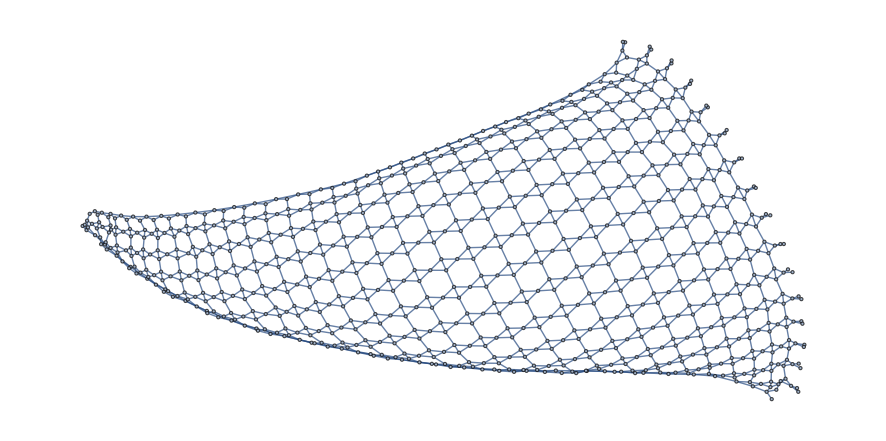

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```

Best initial state string (by observation):

AAAA

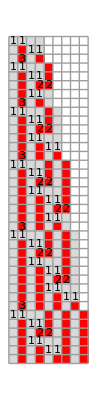
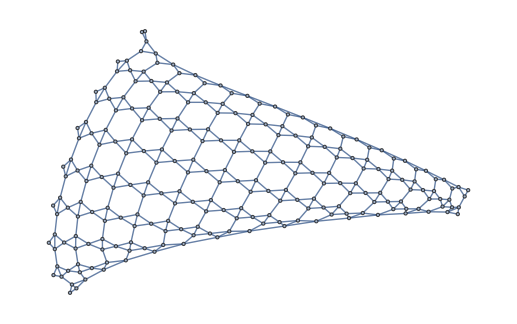
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss=SSS[rs[["RuleSet"]], "AAAA",1000,SSSMax->37,NetMax->233,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->93.,NetSize->{Automatic,269.},SSSSize->{Automatic,220},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

```mathematica
nds=ToNetDifferenceSets[sss["Net"]]
```

{{2,3},{3,4},{1,2},{4,5},{1,2},{1,7},{3,4},{1,2},{5,6},{1,2},{1,2},{4,5},{6,7},{1,2},{7,8},{1,2},{1,2},{6,7},{1,2},{1,10},{6,7},{1,2},{8,9},{1,2},{1,2},{7,8},{1,2},{1,2},{7,8},{9,10},{1,2},{10,11},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{1,2},{1,13},{9,10},{1,2},{11,12},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{12,13},{1,2},{13,14},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,16},{12,13},{1,2},{14,15},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{15,16},{1,2},{16,17},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,19},{15,16},{1,2},{17,18},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{18,19},{1,2},{19,20},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,22},{18,19},{1,2},{20,21},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{21,22},{1,2},{22,23},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,25},{21,22},{1,2},{23,24},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{24,25},{1,2},{25,26},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,28},{24,25},{1,2},{26,27},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{27,28},{1,2},{28,29},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,31},{27,28},{1,2},{29,30},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{30,31},{1,2},{31,32},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,34},{30,31},{1,2},{32,33},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{33,34},{1,2},{34,35},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,37},{33,34},{1,2},{35,36},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{36,37},{1,2},{37,38},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,40},{36,37},{1,2},{38,39},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{39,40},{1,2},{40,41},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,43},{39,40},{1,2},{41,42},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{42,43},{1,2},{43,44},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,46},{42,43},{1,2},{44,45},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{45,46},{1,2},{46,47},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,49},{45,46},{1,2},{47,48},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{48,49},{1,2},{49,50},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,52},{48,49},{1,2},{50,51},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{51,52},{1,2},{52,53},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1},{},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1}}

```mathematica
Position[nds,{49,50}]
```

{{799},{852},{855},{858},{861},{864},{867},{870},{873},{876},{879},{882},{885},{888},{891},{894},{897}}

```mathematica
rsl=ReduceSetList[nds[[1;;897]]]
```

{€_(n$1⊨1)^2[{1+n$1,2+n$1}],{1,2},{4,5},€_(n$3⊨1)^4[€_(n$1⊨1)^2[{1,6-4 n$1-9 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{-9+3 n$2+9 n$3,-8+3 n$2+9 n$3},{1,2},{-6+2 n$2+9 n$3,-5+2 n$2+9 n$3},€^(-2+3 n$3)[€^2[{1,2}],{-7+2 n$2+9 n$3,-6+2 n$2+9 n$3}]],€_(n$1⊨1)^2[{1,2+(-1+n$1) (-1+9 n$3)}],€_(n$2⊨1)^2[{-6+3 n$2+9 n$3,-5+3 n$2+9 n$3},{1,2},{-3+2 n$2+9 n$3,-2+2 n$2+9 n$3},€^(-1+3 n$3)[€^2[{1,2}],{-4+2 n$2+9 n$3,-3+2 n$2+9 n$3}]],€_(n$1⊨1)^2[{1,2 n$1+9 (-1+n$1) n$3}],€_(n$2⊨1)^2[{-3+3 n$2+9 n$3,-2+3 n$2+9 n$3},{1,2},{2 n$2+9 n$3,1+2 n$2+9 n$3},€^(3 n$3)[€^2[{1,2}],{-1+2 n$2+9 n$3,2 n$2+9 n$3}]]],€_(n$1⊨1)^2[{1,2+41 (-1+n$1)}],€_(n$2⊨1)^2[{39+3 (-1+n$2),40+3 (-1+n$2)},{1,2},{41+2 (-1+n$2),42+2 (-1+n$2)},€^13[€^2[{1,2}],{40+2 (-1+n$2),41+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+44 (-1+n$1)}],€_(n$2⊨1)^2[{42+3 (-1+n$2),43+3 (-1+n$2)},{1,2},{44+2 (-1+n$2),45+2 (-1+n$2)},€^14[€^2[{1,2}],{43+2 (-1+n$2),44+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+47 (-1+n$1)}],€_(n$2⊨1)^2[{45+3 (-1+n$2),46+3 (-1+n$2)},{1,2},{47+2 (-1+n$2),48+2 (-1+n$2)},€^15[€^2[{1,2}],{46+2 (-1+n$2),47+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+50 (-1+n$1)}],{48,49},{1,2},{50,51},€^16[€^2[{1,2}],{49,50}]}

```mathematica
rsl[[-7;;-4]]/.{n$3->k,n$2->j,n$1->i, 15->k,45-> 3k,46->3k+1, 47->3k+2, 48->3k+3, 49->3k+4,50->3k+5}
```

{€_(i⊨1)^2[{1,(i-1) (3 k+2)+2}],€_(j⊨1)^2[{3 (j-1)+3 k,3 (j-1)+3 k+1},{1,2},{2 (j-1)+3 k+2,2 (j-1)+3 k+3},€^k[€^2[{1,2}],{2 (j-1)+3 k+1,2 (j-1)+3 k+2}]],€_(i⊨1)^2[{1,(i-1) (3 k+5)+2}],{3 k+3,3 k+4}}

```mathematica
InputForm@%
```

{IndexedConcatenate[{1, 2 + (-1 + i)*(2 + 3*k)}, {i, 1, 2}], 
 IndexedConcatenate[{3*(-1 + j) + 3*k, 1 + 3*(-1 + j) + 3*k}, {1, 2}, 
  {2 + 2*(-1 + j) + 3*k, 3 + 2*(-1 + j) + 3*k}, IndexedConcatenate[
   IndexedConcatenate[{1, 2}, 2], {1 + 2*(-1 + j) + 3*k, 2 + 2*(-1 + j) + 3*k}, k], 
  {j, 1, 2}], IndexedConcatenate[{1, 2 + (-1 + i)*(5 + 3*k)}, {i, 1, 2}], {3 + 3*k, 4 + 3*k}}

```mathematica
{IndexedConcatenate[{1, 2 + (-1 + i)*(2 + 3*k)}, {i, 1, 2}], 
 IndexedConcatenate[{3*(-1 + j) + 3*k, 1 + 3*(-1 + j) + 3*k}, {1, 2}, 
  {2 + 2*(-1 + j) + 3*k, 3 + 2*(-1 + j) + 3*k}, IndexedConcatenate[
   IndexedConcatenate[{1, 2}, 2], {1 + 2*(-1 + j) + 3*k, 2 + 2*(-1 + j) + 3*k}, k], 
  {j, 1, 2}], IndexedConcatenate[{1, 2 + (-1 + i)*(5 + 3*k)}, {i, 1, 2}], {3 + 3*k, 4 + 3*k}}/.k->1//ExpandAll
```

{{1,2},{1,7},{3,4},{1,2},{5,6},{1,2},{1,2},{4,5},{6,7},{1,2},{7,8},{1,2},{1,2},{6,7},{1,2},{1,10},{6,7}}

```mathematica
SequencePosition[nds,{
IndexedConcatenate[
IndexedConcatenate[{1, 2 + (-1 + i)*(2 + 3*k)}, {i, 1, 2}], 
 IndexedConcatenate[{3*(-1 + j) + 3*k, 1 + 3*(-1 + j) + 3*k}, {1, 2}, 
  {2 + 2*(-1 + j) + 3*k, 3 + 2*(-1 + j) + 3*k}, IndexedConcatenate[
   IndexedConcatenate[{1, 2}, 2], {1 + 2*(-1 + j) + 3*k, 2 + 2*(-1 + j) + 3*k}, k], 
  {j, 1, 2}], IndexedConcatenate[{1, 2 + (-1 + i)*(5 + 3*k)}, {i, 1, 2}], {3 + 3*k, 4 + 3*k}
,{k,15,15}]
}//ExpandAll]
```

{{747,847}}

```mathematica
SequencePosition[nds,{
IndexedConcatenate[
IndexedConcatenate[{1, 2 + (-1 + i)*(2 + 3*k)}, {i, 1, 2}], 
 IndexedConcatenate[{3*(-1 + j) + 3*k, 1 + 3*(-1 + j) + 3*k}, {1, 2}, 
  {2 + 2*(-1 + j) + 3*k, 3 + 2*(-1 + j) + 3*k}, IndexedConcatenate[
   IndexedConcatenate[{1, 2}, 2], {1 + 2*(-1 + j) + 3*k, 2 + 2*(-1 + j) + 3*k}, k], 
  {j, 1, 2}], IndexedConcatenate[{1, 2 + (-1 + i)*(5 + 3*k)}, {i, 1, 2}], {3 + 3*k, 4 + 3*k}
,{k,14,15}]
}//ExpandAll]
```

{}

Failed!